```mathematica
(* ::Section::*)(*Folding Harmonics Twin Prime Generator (BBP-Modulated)*)(*Clear any previous definitions*)
ClearAll[bbpDelta,twinPrimesBBP,exportTwinPrimes]

(* ::Subsection::*)
(*BBP-Delta Step Function*)

bbpDelta[n_Integer,kmax_:4]:=Module[{step},step=Total[16^(1-#)/(8 #+Mod[n,7]+1)&/@Range[kmax]];
Floor[step]+1]

(* ::Subsection::*)
(*Twin Prime Generator with BBP-Step Modulation*)

twinPrimesBBP[limit_Integer,kmax_:4]:=Module[{pairs={},n=3},Reap[While[n<limit,If[PrimeQ[n]&&PrimeQ[n+2],Sow[{n,n+2}]];
n+=bbpDelta[n,kmax];]][[2,1]]]

(* ::Subsection::*)
(*Export Twin Primes to File*)

exportTwinPrimes[limit_Integer,file_String]:=Module[{data},data=twinPrimesBBP[limit];
Export[file,data,"Table"];
<|"FilePath"->file,"Count"->Length[data]|>]

(* ::Subsection::*)
(*Usage Example*)

(*Generate and export to file*)
(*Uncomment the following line to run*)
exportTwinPrimes[10^9,"d:/twin_primes_output.txt"]
```

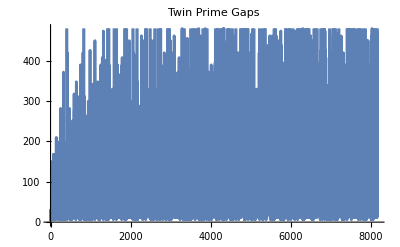

```mathematica
ListPlot[Differences[#[[All,1]]]&@twinPrimesBBP[10^6],PlotLabel->"Twin Prime Gaps",Joined->True]
```

```mathematica
Dataset[<|"FilePath"->"d:/twin_primes_output.txt","Count"->8169|>]
```